# Transformación de Legendre

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Ejemplo analítico

```mathematica
x = Range[-5,5,.1];   (*puntos para graficas*)
x0 = Range[-5,5,.5];   (*Puntos para poner las rectas*)
```

```mathematica
f[x_] := .5*(x-1)^2 + 3  (*Funcion principal*)
df[x_] := .5*2*(x-1)    (*Su derivada*)
u = df[x];   (*u = df/dx*)
lf = u * x - f[x];   (*Transformada de Legendre*)
data = Transpose[{u,lf}];   (*Para graficar correctamente*)
```

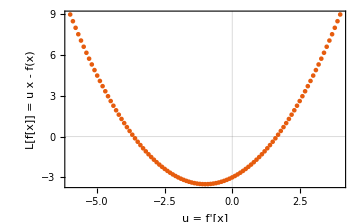

```mathematica
legendrePlot = ListPlot[data,PlotTheme -> "Scientific", 
            FrameLabel -> (Style[#,FontFamily->"Latin Modern Math"]&/@{"u = f'[x]", "L[f[x]] = u x - f(x)"}), 
            ImageSize -> Medium]
```

```mathematica
(*Repetimos lo mismo pero para menos puntos*)
u = df[x0];
lf = u * x0 - f[x0];
data = Transpose[{u,lf}];
data = Map[{#}&,data];   (*Dividimos cada punto para ponerle color*)
```

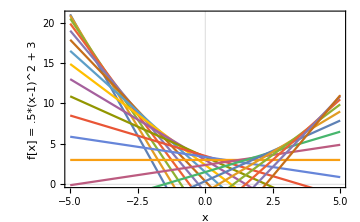
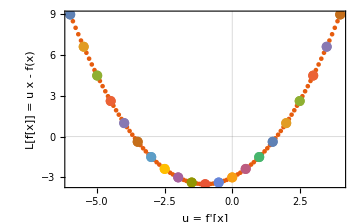

Legendre-quadratic.png

```mathematica
recta = Map[u * (# - x0 ) + f[x0] &, x];
recta = Map[Transpose[{x,#}]&, Transpose[recta]];

legendrePlot = Show[{legendrePlot, ListPlot[data, PlotStyle-> PointSize[.02]]}];
export = Row[{
Show[{ListPlot[Transpose[{x,f[x]}],PlotStyle-> PointSize[.002], PlotTheme -> "Scientific"],
        ListLinePlot[recta]}, FrameLabel -> {"x", "f[x] = .5*(x-1)^2 + 3"}, ImageSize -> Medium],
Show[legendrePlot,PlotRange->Full]
}]
Export["Legendre-quadratic.png",export]
```

#### Función arbitraria (+ GIF)

```mathematica
LegendreTransform[f_] := Module[{x, y, sol, expr},
    sol = Solve[f'[x] == y, x, Reals]; (*writes x in terms of y = f'[x]*)
    expr = FullSimplify[ First[y * x - f[x] /. sol], Element[{x, y}, Reals] ];
            (*Calculates the Legendre transform, a function of y = f'[x] *)
  Evaluate[ expr /. y -> #] & (*Evaluates y as a variable and makes the result a funcion*)]
```

```mathematica
ClearAll[x,f,u]

f[x_] := 2 (x-1)^2 + 3
u[x_] := f'[x]
h[x_, x0_] := u[x0]*(x - x0) + f[x0]
g[y_] := LegendreTransform[f [#] &][y]
```

```mathematica
x0 = 2;
int = {-5, 5}

figs = Table[
Row[{
Show[{
    Plot[f[x], {x, int[[1]], int[[-1]]}, PlotTheme -> "Scientific",  FrameLabel -> {"x", "f[x]"}, ImageSize -> Medium],
    Plot[h[x, x0], {x, Min[{-5, int[[1]]}], int[[-1]]},  PlotStyle -> Dashed]
    },
    PlotRange -> {MinMax[Append[int, 0]],
                    MinMax[Append[Map[h[0, #] &, Range @@ int], Map[f[#] &, Range @@ int]]]},
    Epilog -> {PointSize[Large], Red, 
                    Point[{0, h[0, x0]}],  
                    Inset[h[0, x0], {.5, h[0, x0]}],
                Blue, 
                    Point[{x0, f[x0]}], 
                    Inset["f'[x0] = " <> ToString@u[x0], {x0, f[x0] - 5}]
              }
    ],
Plot[g[y], {y, u@int[[1]], u@int[[-1]]}, PlotTheme -> "Scientific", 
            FrameLabel -> {"u = f'[x]", "L[f[x]] = g[u]"}, 
            ImageSize -> Medium,
         Epilog -> {PointSize[Large], Red, Point[{u[x0], g[u[x0]]}], 
                   Inset["(" <> ToString[u[x0]] <> "," <> ToString@g[u[x0]] <> ")", {u[x0], g[u[x0]] - 1}]
                   }]
    }],
{x0, int[[1]], int[[-1]],.1}];
```

{-5,5}

```mathematica
Export["Legendre-quadratic.gif",figs, "DisplayDurations" -> .15, "AnimationRepetitions" -> ∞]
```

Legendre-quadratic.gif

```mathematica
x = Range[-5,5,.1];
f = Exp[x];
u = Differences[f]/Differences[x];
x = Drop[x,-1];
f = Drop[f,-1];
```

```mathematica
sin2[x_]:=Sin[x]^2
Map[{#}&, x]
```

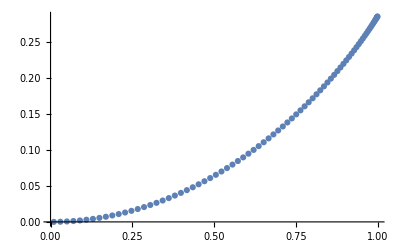

```mathematica
ListPlot[ NLegendreTransform[Sin[#]^2&,{0,Pi/4,.01}]]

NLegendreTransform[func_,{xi_,xf_,h_}]:= Module[{x,f,u},
  x = Range[xi,xf, h];
  f = func[x];
  u = Differences[f]/Differences[x];
  x = Drop[x,-1];
  f = Drop[f,-1]; 
  Transpose[{u,u*x-f}]
]
```

```mathematica
NLegendreTransformList[x_List,y_List]:= Module[{u,x0,f},
  u = Differences[y]/Differences[x];
  x0 = Drop[x,-1];
  f = Drop[y,-1]; 
  Transpose[{u,u*x0-f}]
]
```

```mathematica
x = Range[.025,5,.1];
y = -Log[x];
```

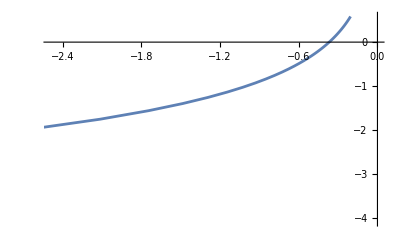

```mathematica
NLegendreTransformList[x,y]//ListLinePlot
```